A1+f1/(E1^2-h^2 ω^2)+f2/(E2^2-h^2 ω^2)

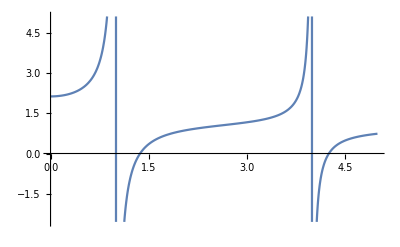

```mathematica
polzMdl=A1+f1/(E1^2-h^2 ω^2)+f2/(E2^2-h^2 ω^2)
Plot[polzMdl/.{A1->1,f1->1,f2->2,E1->1,E2->4,h->1},{ω,0,5}]
```

## 2 component model

```mathematica
Real[polzMdl/.{A1->1,f1->1,f2->2,E1->1,E2->4,ω->1.5,h->1}]
```

Real[0.345455]

Get the tune out freq from the model

```mathematica
ToFreqTwoLevel=Solve[0==polzMdl/.{A1->0},ω]
ToFreqTwoLevel=ω/.ToFreqTwoLevel[[2]]
FullSimplify[ToFreqTwoLevel,Assumptions->{h>0}]
```

{{ω→-(√(E2^2 f1+E1^2 f2))/(√(f1 h^2+f2 h^2))},{ω→(√(E2^2 f1+E1^2 f2))/(√(f1 h^2+f2 h^2))}}

(√(E2^2 f1+E1^2 f2))/(√(f1 h^2+f2 h^2))

(√(E2^2 f1+E1^2 f2))/(√(f1+f2) h)

replace one of the osc strengths with X1 times f1 so that we can express the answer in terms of the osc strength ratio

```mathematica
ToFreqTwoLevel=Simplify[ToFreqTwoLevel/.f2->X1 f1]
```

(√(f1 (E2^2+E1^2 X1)))/(√(f1 h^2 (1+X1)))

Get the ratio from the tune out and the transition freqs

```mathematica
RatioVal=Solve[ωto==ToFreqTwoLevel,X1]
RatioVal=FullSimplify[RatioVal, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals, ωto∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0, ωto>0}]
```

{{X1→(-E2^2+h^2 ωto^2)/(E1^2-h^2 ωto^2)}}

{{X1→(-E2^2+h^2 ωto^2)/(E1^2-h^2 ωto^2)}}

Get the derivative of this ratio with the tune out freq

```mathematica
DerivTOWithX=D[ToFreqTwoLevel,X1]
DerivTOWithX=FullSimplify[DerivTOWithX, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals,A1∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0,A1>0,f1>0}]
```

(E1^2 f1)/(2 √(f1 h^2 (1+X1)) √(f1 (E2^2+E1^2 X1)))-(f1 h^2 √(f1 (E2^2+E1^2 X1)))/(2 (f1 h^2 (1+X1))^(3/2))

((E1-E2) (E1+E2))/(2 h (1+X1)^(3/2) √(E2^2+E1^2 X1))

Use this to find the fractional uncert of X given some uncert in the tune out freq

```mathematica
FracUncX=(1/DerivTOWithX)δωTo/X1/.RatioVal[[1]]
Simplify[FracUncX, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals, ωto∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0, ωto>0}]
```

(2 h δωTo (E1^2-h^2 ωto^2) (1+(-E2^2+h^2 ωto^2)/(E1^2-h^2 ωto^2))^(3/2) √(E2^2+(E1^2 (-E2^2+h^2 ωto^2))/(E1^2-h^2 ωto^2)))/((E1-E2) (E1+E2) (-E2^2+h^2 ωto^2))

(2 (E1^2-E2^2) h^2 δωTo ωto)/((E1^2-h^2 ωto^2) (-E2^2+h^2 ωto^2))

## 2 component model for R

What are our number like if we calculate the ratio of the dipole matrix  elements instead of the oscillator strengths

```mathematica
polzMdl=A1+1/ℏ(2T1 D1)/(T1^2-ω^2)+1/ℏ(2 T2 D2)/(T2^2-ω^2)
```

A1+(2 D1 T1)/((T1^2-ω^2) ℏ)+(2 D2 T2)/((T2^2-ω^2) ℏ)

```mathematica
Real[polzMdl/.{A1->1,D1->1,D2->2,T1->1,T2->4,ω->1.5,ℏ->1}]
```

Real[0.563636]

```mathematica
ToFreqTwoLevel=Solve[0==polzMdl/.{A1->0},ω]
ToFreqTwoLevel=ω/.ToFreqTwoLevel[[2]]
FullSimplify[ToFreqTwoLevel,Assumptions->{ℏ>0}]
```

{{ω→-(√(D2 T1^2 T2+D1 T1 T2^2))/(√(D1 T1+D2 T2))},{ω→(√(D2 T1^2 T2+D1 T1 T2^2))/(√(D1 T1+D2 T2))}}

(√(D2 T1^2 T2+D1 T1 T2^2))/(√(D1 T1+D2 T2))

(√(T1 T2 (D2 T1+D1 T2)))/(√(D1 T1+D2 T2))

```mathematica
ToFreqTwoLevel=Simplify[ToFreqTwoLevel/.D2->R D1]
```

(√(D1 T1 T2 (R T1+T2)))/(√(D1 (T1+R T2)))

```mathematica
RatioVal=Solve[ωto==ToFreqTwoLevel,R]
RatioVal=FullSimplify[RatioVal, Assumptions->{ℏ∈Reals,T1∈Reals,T2∈Reals, ωto∈Reals,D1∈Reals,D2∈Reals,R∈Reals,ℏ>0,T1>0,T2>0, ωto>0}]
```

{{R→(-T1 T2^2+T1 ωto^2)/(T2 (T1^2-ωto^2))}}

{{R→(T1 (-T2^2+ωto^2))/(T2 (T1^2-ωto^2))}}

```mathematica
DerivTOWithR=D[ToFreqTwoLevel,R]
DerivTOWithR=FullSimplify[DerivTOWithR, Assumptions->{ℏ∈Reals,T1∈Reals,T2∈Reals, ωto∈Reals,D1∈Reals,D2∈Reals,R∈Reals,ℏ>0,D1>0,T2>0,T1>0, ωto>0}]
```

-(D1 T2 √(D1 T1 T2 (R T1+T2)))/(2 (D1 (T1+R T2))^(3/2))+(D1 T1^2 T2)/(2 √(D1 T1 T2 (R T1+T2)) √(D1 (T1+R T2)))

((T1-T2) (T1+T2))/(2 √(1/T1+R/T2) (T1+R T2)^(3/2))

```mathematica
FracUncR=(1/DerivTOWithR)δωTo/R/.RatioVal[[1]]
Simplify[FracUncR, Assumptions->{ℏ∈Reals,T1∈Reals,T2∈Reals, ωto∈Reals,D1∈Reals,D2∈Reals,R∈Reals,ℏ>0,D1>0,T2>0,T1>0, ωto>0}]
```

(2 T2 δωTo (T1^2-ωto^2) (T1+(T1 (-T2^2+ωto^2))/(T1^2-ωto^2))^(3/2) √(1/T1+(T1 (-T2^2+ωto^2))/(T2^2 (T1^2-ωto^2))))/(T1 (T1-T2) (T1+T2) (-T2^2+ωto^2))

(2 (T1^2-T2^2) δωTo ωto)/((T1^2-ωto^2) (-T2^2+ωto^2))

## 3 component system

```mathematica
polzMdl=A1+f1/(E1^2-h^2 ω^2)+f2/(E2^2-h^2 ω^2)
```

A1+f1/(E1^2-h^2 ω^2)+f2/(E2^2-h^2 ω^2)

Now lets try this again but with the offset

```mathematica
ToFreqTwoLevel=Solve[0==polzMdl,ω]
```

{{ω→-(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)-(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))/(A1 h^4)))/(√2)},{ω→(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)-(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))/(A1 h^4)))/(√2)},{ω→-(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)+(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))/(A1 h^4)))/(√2)},{ω→(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)+(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))/(A1 h^4)))/(√2)}}

Which of these roots do i want?? 
ok looks like the second

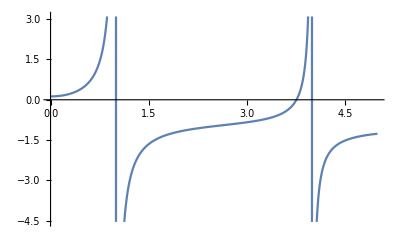

{{ω→-3.76051},{ω→3.76051},{ω→0.-0.37607 ⅈ},{ω→0.+0.37607 ⅈ}}

```mathematica
Plot[polzMdl/.{A1->-1,f1->1,f2->2,E1->1,E2->4,h->1},{ω,0,5}]
N[ToFreqTwoLevel/.{A1->-1,f1->1,f2->2,E1->1,E2->4,h->1}]
```

```mathematica
ToFreqThreeComp=ω/.ToFreqTwoLevel[[2]]
ToFreqThreeComp=ToFreqThreeComp/.{f2->X1 f1,A1->X2 f1}
```

(√(E1^2/h^2+E2^2/h^2+f1/(A1 h^2)+f2/(A1 h^2)-(√((A1^2 E1^4-2 A1^2 E1^2 E2^2+A1^2 E2^4+2 A1 E1^2 f1-2 A1 E2^2 f1+f1^2-2 A1 E1^2 f2+2 A1 E2^2 f2+2 f1 f2+f2^2) h^4))/(A1 h^4)))/(√2)

(√(E1^2/h^2+E2^2/h^2+1/(h^2 X2)+X1/(h^2 X2)-(√(h^4 (f1^2+2 f1^2 X1+f1^2 X1^2+2 E1^2 f1^2 X2-2 E2^2 f1^2 X2-2 E1^2 f1^2 X1 X2+2 E2^2 f1^2 X1 X2+E1^4 f1^2 X2^2-2 E1^2 E2^2 f1^2 X2^2+E2^4 f1^2 X2^2)))/(f1 h^4 X2)))/(√2)

```mathematica
Solve[ωto==ToFreqThreeComp,X1]
```

{{X1→-((E2^2-h^2 ωto^2) (-1-E1^2 X2+h^2 X2 ωto^2))/(-E1^2+h^2 ωto^2)}}

```mathematica
ToFreqThreeComp=FullSimplify[ToFreqThreeComp, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals,A1∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0,A1>0,f1>0}]
```

(√((1+X1+(E1^2+E2^2) X2-√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2))/(h^2 X2)))/(√2)

```mathematica
DerivTOWithX=FullSimplify[D[ToFreqThreeComp,X1], Assumptions->{h∈Reals,E1∈Reals,E2∈Reals,A1∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0,A1>0,f1>0}]
```

(1-(1+X1-E1^2 X2+E2^2 X2)/(√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2)))/(2 √2 h X2 √((1+X1+(E1^2+E2^2) X2-√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2))/X2))

```mathematica
FracUncX=(1/DerivTOWithX)δωTo/X1/.RatioVal[[1]]
Simplify[FracUncX, Assumptions->{h∈Reals,E1∈Reals,E2∈Reals, ωto∈Reals,X1∈Reals,X2∈Reals,f1∈Reals,h>0,E1>0,E2>0, ωto>0}]
```

(2 √2 h X2 √((1+X1+(E1^2+E2^2) X2-√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2))/X2) δωTo)/(X1 (1-(1+X1-E1^2 X2+E2^2 X2)/(√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2))))

(2 √2 h X2 √((1+X1+(E1^2+E2^2) X2-√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2))/X2) δωTo)/(X1-(X1 (1+X1-E1^2 X2+E2^2 X2))/(√(X1^2+X1 (2-2 E1^2 X2+2 E2^2 X2)+(1+(E1-E2) (E1+E2) X2)^2)))